# Tutorial 2 - Lecture

```mathematica
Solve[x^2 + a x -1 ==0, x]
```

{{x→1/2 (-a-√(4+a^2))},{x→1/2 (-a+√(4+a^2))}}

```mathematica
Eqn1[x_, y_]:= x + y ==0 
Eqn2[x_, y_]:= x- y ==2
sysEqn = Eqn1[x, y] && Eqn2[x, y];
```

```mathematica
Solve[sysEqn, {x, y}]
Solve[x + y ==0 &&x- y ==2 , {x, y}]
```

{{x→1,y→-1}}

{{x→1,y→-1}}

```mathematica
Solve[(x^2 + 2)(x^2 - 2 )==0, x∈ Reals]
```

{{x→-√2},{x→√2}}

```mathematica
diffEqn1[f_, t_]:= f'[t] == r f[t]
```

```mathematica
DSolve[diffEqn1[f, t], f[t], t]
solDiff = DSolve[ {diffEqn1[f, t], f[0]== F}, f[t], t]
diffEqn1[f, t]/.solDiff[[1]]
```

{{f[t]→ⅇ^(r t) C[1]}}

{{f[t]→ⅇ^(r t) F}}

f'[t]==ⅇ^(r t) F r

```mathematica
expRes = Series[Exp[x], {x, 0, 10}]
Normal[expRes]
serRes = Series[f[x], {x, a, 2}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+O[x-a]^3

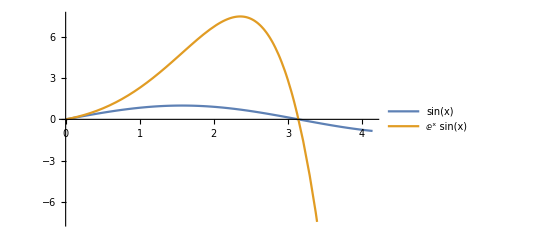

```mathematica
plot1 = Plot[{Sin[x], E^x * Sin[x]}, {x, 0, π+1}, PlotLegends->"Expressions"]
(*Export["Plot1.pdf", plot1]
Directory[]*)
```

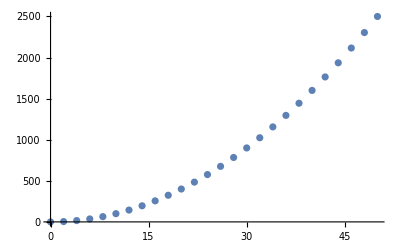

```mathematica
dataStruct=Table[{i,i^2} ,{i, 0, 50, 2}];
plot2 = ListPlot[dataStruct]
(*Export["Plot2.pdf", plot2]*)
```

# Tutorial 2 - Exercises

### Ex1)

```mathematica
(* To specify the system of equations we use the && operator, and to specify for which variables to solve the system we declare them in the {} brackets. *)
Solve[x + b y - c z ==0 && x+c z==5 && a x - b y ==4, {x, y, z}]
```

### Ex2)

```mathematica
(* To specify the >0 condition we need to again use the && operator (i.e. in effect we're treating the >0 conditions as self sufficent equations), and the ϵ argument followed by either Intergers/ Reals will then ensure that the solutions are from the required set *)
Solve[x^2 + 2y^2 == 3681 && x>0 && y>0, {x∈ Integers, y∈Integers}]
Solve[x^2 + 2y^2 == 3681 && x>0 && y>0, {x∈ Integers, y∈Reals}]
```

### Ex3)

```mathematica
(*Similar to using the && operator we can just define a list of equations that we then pass to the NDSove[] function to NUMERICALLY SOLVE THE SYSTEM due to the high complexity (Note that if we tried to use the analytical solver DSolve[] Mathematica would just go on forever).*)
eqns = {
μ D[g1[μ], μ] ==(41/6)(g1[μ]^3/(16 π^2)),
μ D[g2[μ], μ]== -( 19/6)(g2[μ]^3/(16 π^2)),
μ D[g3[μ], μ]==-7  (g3[μ]^3/(16 π^2)),
μ D[y[μ], μ]==((9y[μ])/2-(17 g1[μ]^2)/12-(9 g2[μ]^2)/4-8 g3[μ]^2)y[μ]/(16 π^2),
μ D[λ[μ], μ]==(1/(16 π^2))((3 g1[μ]^4)/8+(3 g1[μ]^2 g2[μ]^2)/4+(9 g2[μ]^4)/8-6 y[μ]^4 - (3 g1[μ]^2+9 g2[μ]^2-12 y[μ]^2)λ[μ]+24 λ[μ]^2)
};

(*ND solve analogously to Solve requires a set of initial coniditions (which our exercise provides), the functions for which we want to solve the system for and the variable and its range to be solved for. Note that we then get a set of interpolating polynomials as the solutions. *)
μMax = 10^5;
numSoln = NDSolve[{eqns, g1[80]==0.35, g2[80]==0.62, g3[80]==1.22, y[80]==1, λ[80]==0.13},{g1, g2, g3, λ, y}, {μ, 80,μMax}];

(*We then use the interpolating polynomial solutions to plot and inspect where λ hits 0, and find the numerical solution using FindRoot[]*)
Plot[{λ[μ]}/.numSoln, {μ, 9*10^4, μMax}]
μSoln = FindRoot[(λ[μ])/.numSoln[[1, 4]], {μ, 100}]
λ[μ]/.numSoln/.μSoln
```

### Ex4)

```mathematica
(*The different approximations are found using Series[], and then Normal[] (to eliminate the O(x^n) argument). Using a For loop we then generate our Print statements for the different approximations at the different x_i values.*)
approx1 = Normal[Series[Sin[x], {x, 0, 1}]];
approx3 = Normal[Series[Sin[x], {x, 0, 3}]];
approx5 = Normal[Series[Sin[x], {x, 0, 5}]];


For[xi=1.0, xi≤2.5, xi=xi+0.5,

Print["Sin(x) value :", Sin[xi]];
Print["Sin(x) To O(x^1) is accurate to : ", Abs[(Sin[x]-approx1)/Sin[x]*100] /.{x->xi}, "% at x=", xi];
Print["Sin(x) To O(x^3) is accurate to : ", Abs[(Sin[x]-approx3)/Sin[x]*100] /.{x->xi}, "% at x=", xi];
Print["Sin(x) To O(x^5) is accurate to : ", Abs[(Sin[x]-approx5)/Sin[x]*100] /.{x->xi}, "% at x=", xi];
Print[""]
]

(*To visualise the graphical approximations we create a Plot[] with all the expressions , and a ListPlot[] with all the specific points. To show both on the same axis we use Show[...] *)
plt1 = Plot[{approx1, approx3, approx5, Sin[x]}, {x, 0, π},PlotLegends->"Expressions" ];
lstPlt = ListPlot[{{1.5, Sin[x]/.{x->1.5}}, {1.5, approx1/.{x->1.5}}, {1.5, approx3/.{x->1.5}}, {1.5, approx5/.{x->1.5}}}];

Show[plt1, lstPlt]
```